The longest-running sim to estimate across the first 50 iterations took:
	82.5 hours for single-individual estimates
	67.0 hours for pooled-individual estimates (faster, because more data makes the likelihood surface easier to explore?)

```mathematica
dataSingle = Import["single_ind_estimates_per_rep_d_1000.tsv","Dataset",HeaderLines-> 0];
dataPooled = Import["pooled_ind_estimates_per_rep_d_1000.tsv","Dataset",HeaderLines-> 0];
```

```mathematica
kappasSingle = #[[1;;19]]&/@dataSingle;
gammasSingle = #[[20;;20+19-1]] &/@ dataSingle;
LsSingle = #[[-1]]&/@dataSingle;

kappasPooled = #[[1;;19]]&/@dataPooled;
gammasPooled = #[[20;;20+19-1]] &/@ dataPooled;
LsPooled = #[[-1]]&/@dataPooled;
```

```mathematica
truthChrKappaGamma = {{1,0.00145756486,0.00235996959},{2,0.00180727905,0.00342621318},{3,0.00186536342,0.0035423356},{4,0.00161298296,0.00225109243},{5,0.00194717866,0.0031020052},{6,0.00170580009,0.00271860563},{7,0.00167423386,0.00262167771},{8,0.0023152398,0.0037924023},{9,0.00173683272,0.0035986003},{10,0.00196466475,0.00395571965},{11,0.00174678502,0.00279145592},{12,0.00175203665,0.00358232934},{13,0.00189861553,0.00443149452},{14,0.00192549761,0.0039928514},{15,0.00160604398,0.00211168309},{16,0.00185130817,0.00380296933},{17,0.00180849818,0.00292979399},{18,0.0021214869,0.00257933143},{19,0.00268619142,0.00460506687}};
```

```mathematica
truthKappas =  {#[[1]],#[[2]]}&/@truthChrKappaGamma;
truthGammas = {#[[1]],#[[3]]}&/@truthChrKappaGamma;
truthLs = {{1,108.399686}};
```

```mathematica
chrStrings = TextString[#]&/@Range[19]//InputForm
```

{"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", "11", "12", "13", "14", "15", "16", "17", "18", "19"}

```mathematica
chrStrings = {"1", "2", "3", "4", "5", "6", "7", "8", "9", "10", "11", "12", "13", "14", "15", "16", "17", "18", "19"}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
truthKappas
```

{{1,0.00145756},{2,0.00180728},{3,0.00186536},{4,0.00161298},{5,0.00194718},{6,0.0017058},{7,0.00167423},{8,0.00231524},{9,0.00173683},{10,0.00196466},{11,0.00174679},{12,0.00175204},{13,0.00189862},{14,0.0019255},{15,0.00160604},{16,0.00185131},{17,0.0018085},{18,0.00212149},{19,0.00268619}}

```mathematica
19*2
```

38

```mathematica
plotKappas = MapThread[{#1,#2[[2]]}&,{Range[2,19*2,2],truthKappas}]
plotGammas = MapThread[{#1,#2[[2]]}&,{Range[1,19*2,2],truthGammas}]
```

{{2,0.00145756},{4,0.00180728},{6,0.00186536},{8,0.00161298},{10,0.00194718},{12,0.0017058},{14,0.00167423},{16,0.00231524},{18,0.00173683},{20,0.00196466},{22,0.00174679},{24,0.00175204},{26,0.00189862},{28,0.0019255},{30,0.00160604},{32,0.00185131},{34,0.0018085},{36,0.00212149},{38,0.00268619}}

{{1,0.00235997},{3,0.00342621},{5,0.00354234},{7,0.00225109},{9,0.00310201},{11,0.00271861},{13,0.00262168},{15,0.0037924},{17,0.0035986},{19,0.00395572},{21,0.00279146},{23,0.00358233},{25,0.00443149},{27,0.00399285},{29,0.00211168},{31,0.00380297},{33,0.00292979},{35,0.00257933},{37,0.00460507}}

```mathematica
empty = Table[{0},{i,1,Length[Transpose[gammasPooled]]}]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

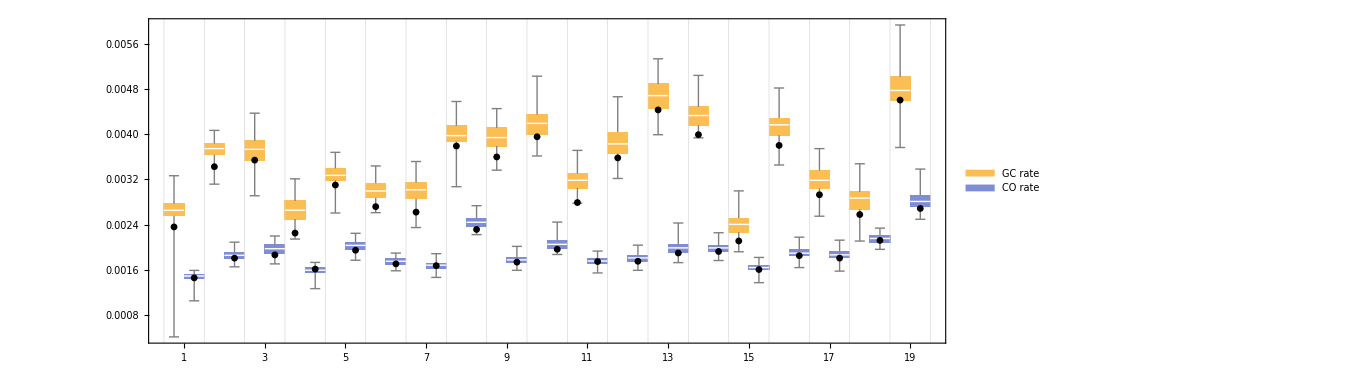

```mathematica
pooledGCandCOplot = Show[
BoxWhiskerChart[
MapThread[{#1,#2}&,{Normal@Transpose[gammasPooled],Normal@Transpose[kappasPooled]}],
PlotRange->{{2,19*2-1},{0,All}},
Ticks->None,
ChartLabels->{chrStrings,{None}}(*ChartLabels->{chrStrings,{None,None,None,None}}*),
BarSpacing->{0,0},
AspectRatio->9/16/(1.5),
ChartLegends->{"GC rate","CO rate"},
LabelStyle->Directive[12,Bold,Thick],
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],
ImageSize->Large],
ListPlot[plotKappas,PlotMarkers->{Automatic,Small},PlotStyle->Black],
ListPlot[plotGammas,PlotMarkers->{Automatic,Small},PlotStyle->Black],
ImageSize->1000,GridLines->{Range[0.5,19*2+0.5,2],{0}},GridLinesStyle->{Directive[Thick,Lighter@Lighter@Gray],{White}}
]
```

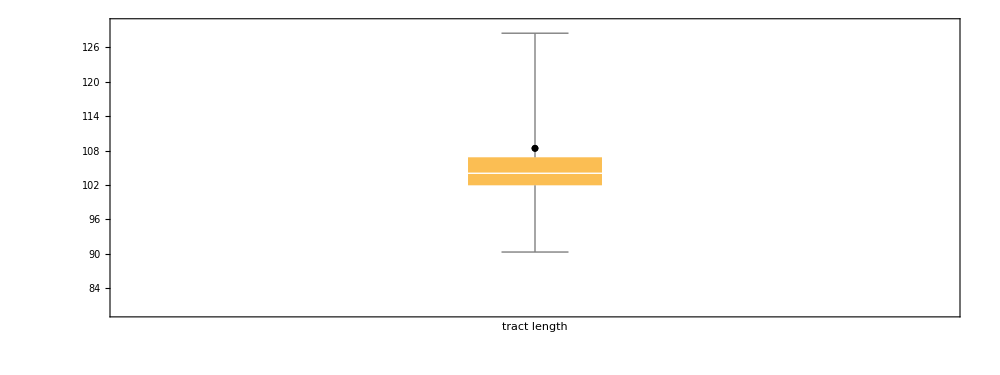

```mathematica
pooledLplot = Show[
BoxWhiskerChart[LsPooled,BarOrigin->Bottom,
LabelStyle->Directive[12,Bold,Thick],
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],
FrameLabel->{"tract length",""},
ImageSize->Medium,PlotRange->All,
AspectRatio->9/16/(1.5)],
ListPlot[truthLs,PlotStyle->Black,PlotMarkers->{Automatic,Small}],
ImageSize->1000,
PlotRange->{All,{80,130}}
]
```

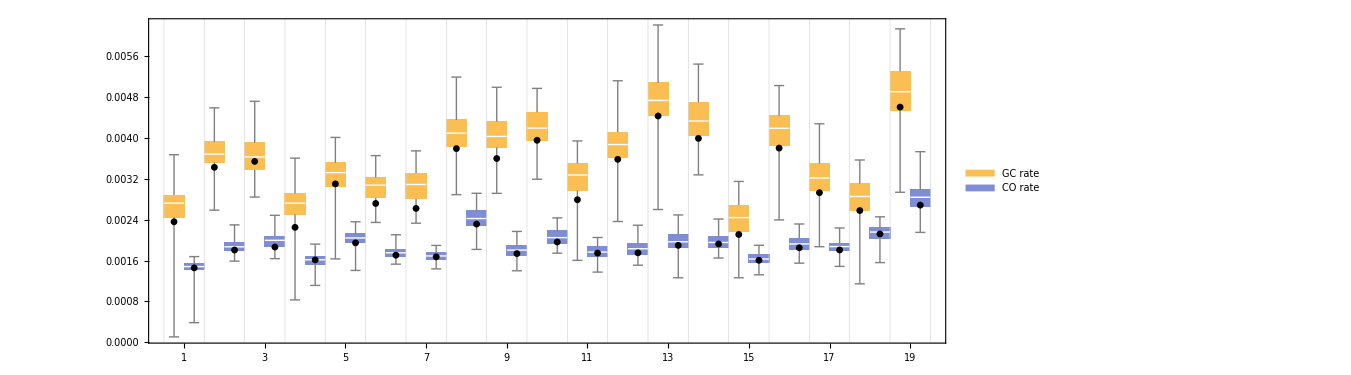

```mathematica
singleGCandCOplot = Show[
BoxWhiskerChart[
MapThread[{#1,#2}&,{Normal@Transpose[gammasSingle],Normal@Transpose[kappasSingle]}],
PlotRange->{{2,19*2-1},{0,All}},
Ticks->None,
ChartLabels->{chrStrings,{None}}(*ChartLabels->{chrStrings,{None,None,None,None}}*),
BarSpacing->{0,0},
AspectRatio->9/16/(1.5),
ChartLegends->{"GC rate","CO rate"},
LabelStyle->Directive[12,Bold,Thick],
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],
ImageSize->Large],
ListPlot[plotKappas,PlotMarkers->{Automatic,Small},PlotStyle->Black],
ListPlot[plotGammas,PlotMarkers->{Automatic,Small},PlotStyle->Black],
ImageSize->1000,GridLines->{Range[0.5,19*2+0.5,2],{0}},GridLinesStyle->{Directive[Thick,Lighter@Lighter@Gray],{White}}
]
```

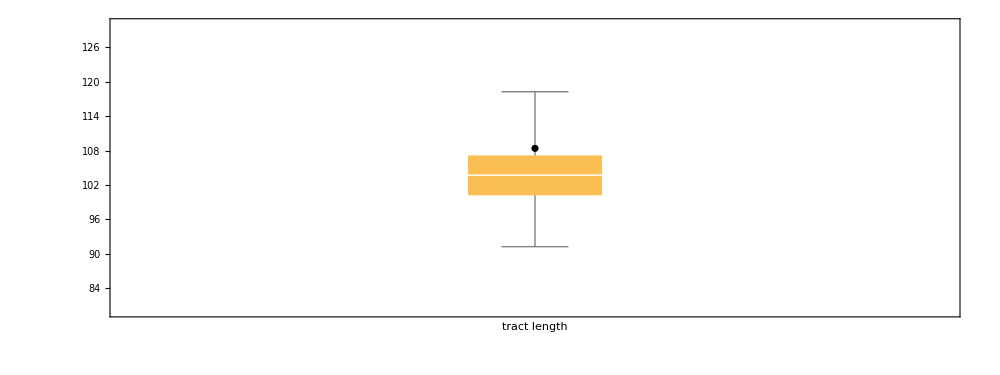

```mathematica
singleLplot = Show[
BoxWhiskerChart[LsSingle,BarOrigin->Bottom,
LabelStyle->Directive[12,Bold,Thick],
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],
FrameLabel->{"tract length",""},
ImageSize->Medium,PlotRange->All,
AspectRatio->9/16/(1.5)],
ListPlot[truthLs,PlotStyle->Black,PlotMarkers->{Automatic,Small}],
ImageSize->1000,
PlotRange->{All,{80,130}}
]
```